```mathematica
(*DumpSave["graphsgenerated.mx","Global`"];*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["graphsgenerated.mx"];
```

```mathematica
SymmetricPermutations[A_]:= Module[{get,perms, len = Length[A],Ain=A,syms,symsel},
get =  Flatten[Table[Table[Ain[[i,j]],{j,i+1,len}],{i,1,len}]];
perms = Permutations[get];
upperTriangular[v_,n_]:=Module[{i=0},Array[If[#≥#2,0,v[[++i]]]&,{n,n}]];
syms=Table[upperTriangular[perms[[i]],Length[A]]+Transpose[upperTriangular[perms[[i]],Length[A]]],{i,1,Length[perms]}];
symsel=Select[syms,Times@@Total[#]!=0&];
Return[symsel];]
```

```mathematica
H[G_,γ_]:=SparseArray[(-G+DiagonalMatrix[Total[G,{2}]])*γ];
LindbladSet[H_]:=Select[Table[SparseArray[Flatten[ArrayReshape[Table[{{i,j}->Sqrt[Abs[H[[i]][[j]]]]},{i,1,Length[H]},{j,Length[H]}],{1,Length[H]^2}]][[i]],{Length[H],Length[H]}],{i,Length[H]^2}],Length[ArrayRules[#]]>1&]; 
Trapping[H_,κ_,traps_]:=κ SparseArray[Table[{traps[[i]],traps[[i]]}-> 1,{i,Length[traps]}],{Length[H],Length[H]}];
Recombination[H_,Γ_]:=DiagonalMatrix[Table[Γ,{i,Length[H]}]];
SuperOperator[H_,Trapping_,Recombination_,LindbladSet_,ω_,ℏ_]:=SparseArray[(1-ω)-I/ℏ(KroneckerProduct[H,IdentityMatrix[Length[H]]]-KroneckerProduct[IdentityMatrix[Length[H]],Transpose[H]])]+SparseArray[-1/ℏ(KroneckerProduct[Trapping,IdentityMatrix[Length[Trapping]]] + KroneckerProduct[IdentityMatrix[Length[Trapping]], Trapping])]+SparseArray[-1/ℏ(KroneckerProduct[Recombination,IdentityMatrix[Length[Recombination]]] + KroneckerProduct[IdentityMatrix[Length[Recombination]], Recombination])]+SparseArray[ω Sum[KroneckerProduct[Conjugate[LindbladSet[[i]]],LindbladSet[[i]]]-1/2(KroneckerProduct[IdentityMatrix[Length[H]],ConjugateTranspose[LindbladSet[[i]]].LindbladSet[[i]]]+KroneckerProduct[Transpose[LindbladSet[[i]]].Conjugate[LindbladSet[[i]]],IdentityMatrix[Length[H]]]),{i,Length[LindbladSet]}]];
η[Trapping_,SuperOperator_,ρ0_,ℏ_]:=-2/ℏ Total[Chop[Diagonal[ArrayReshape[SparseArray[KroneckerProduct[Trapping,IdentityMatrix[Length[Trapping]]].Inverse[SuperOperator].Flatten[ρ0]],{Length[Trapping],Length[Trapping]}]]]];
ηcoherent[Recombination_,Trapping_,Coherent_,SuperOperator_,ρ0_,ℏ_,ω_]:=-2/ℏ Total[Chop[Diagonal[ArrayReshape[KroneckerProduct[Recombination,IdentityMatrix[Length[Recombination]]].Inverse[SparseArray[-1/ℏ(KroneckerProduct[Trapping,IdentityMatrix[Length[Trapping]]] + KroneckerProduct[IdentityMatrix[Length[Trapping]], Trapping])]+SparseArray[-1/ℏ(KroneckerProduct[Recombination,IdentityMatrix[Length[Recombination]]] + KroneckerProduct[IdentityMatrix[Length[Recombination]], Recombination])]].SparseArray[(1-ω)-I/ℏ(KroneckerProduct[Coherent,IdentityMatrix[Length[Coherent]]]-KroneckerProduct[IdentityMatrix[Length[Coherent]],Transpose[Coherent]])].Inverse[SuperOperator].Flatten[ρ0],{Length[Recombination],Length[Recombination]}]]]];
ηscattering[Recombination_,Trapping_,LindbladSet_,SuperOperator_,ρ0_,ℏ_,ω_]:=-2/ℏ Total[Chop[Diagonal[ArrayReshape[KroneckerProduct[Recombination,IdentityMatrix[Length[Recombination]]].Inverse[SparseArray[-1/ℏ(KroneckerProduct[Trapping,IdentityMatrix[Length[Trapping]]] + KroneckerProduct[IdentityMatrix[Length[Trapping]], Trapping])]+SparseArray[-1/ℏ(KroneckerProduct[Recombination,IdentityMatrix[Length[Recombination]]] + KroneckerProduct[IdentityMatrix[Length[Recombination]], Recombination])]].(SparseArray[ω Sum[KroneckerProduct[Conjugate[LindbladSet[[i]]],LindbladSet[[i]]]-1/2(KroneckerProduct[IdentityMatrix[Length[Recombination]],ConjugateTranspose[LindbladSet[[i]]].LindbladSet[[i]]]+KroneckerProduct[Transpose[LindbladSet[[i]]].Conjugate[LindbladSet[[i]]],IdentityMatrix[Length[Recombination]]]),{i,Length[LindbladSet]}]]).Inverse[SuperOperator].Flatten[ρ0],{Length[Recombination],Length[Recombination]}]]]];

QuantumStochasticWalk[SuperOperator_,ρ0_,t_]:=ArrayReshape[MatrixExp[SuperOperator t,Flatten[ρ0]],{Length[ρ0],Length[ρ0]}];
```

#### Universal Constants

```mathematica
κ=0.01;
γ=0.2;
Γ=0.001;
ℏ=1;
ω=0.1;
```

#### FMO Topology

```mathematica
FMO =  ({{0, 1, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 0, 0, 0}, {0, 0, 1, 0, 1, 0, 1}, {0, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 1, 0, 1, 0}});
```

```mathematica
syms=SymmetricPermutations[FMO];
perms=Table[syms[[i]],{i,1,Length[syms]}];
perms = Select[perms,Length[ConnectedComponents[AdjacencyGraph[#]]]<2&];
perms =Select[perms,Length[FindShortestPath[AdjacencyGraph[#],6,3]]==4&];
perms =DeleteDuplicates[perms,IsomorphicGraphQ[AdjacencyGraph[#1],AdjacencyGraph[#2]]&];
```

```mathematica
FMOcoherent=H[FMO,γ];
FMOLkSet=LindbladSet[FMOcoherent];
FMOexits={3};
FMOtrapping=Trapping[FMO,κ,FMOexits];
FMOrecombination=Recombination[FMO,Γ];
FMOM = SuperOperator[FMOcoherent,FMOtrapping,FMOrecombination,FMOLkSet,ω,ℏ];
FMOρ0=SparseArray[{6,6}-> 1,{Length[FMO],Length[FMO]}];
```

```mathematica
Manipulate[AdjacencyGraph[FMO,VertexSize->Table[i-> Diagonal[Chop[QuantumStochasticWalk[FMOM,FMOρ0,t]]][[i]],{i,Length[FMO]}],VertexLabels->"Name", VertexStyle->Red,PlotLabel->"FMO ρ(t)"],{t,0,60,AnimationRate->2,ControlType-> Animator,RefreshRate-> 30}]
```

AdjacencyGraph::matsq: Argument FMO at position 1 is not a non-empty square matrix.

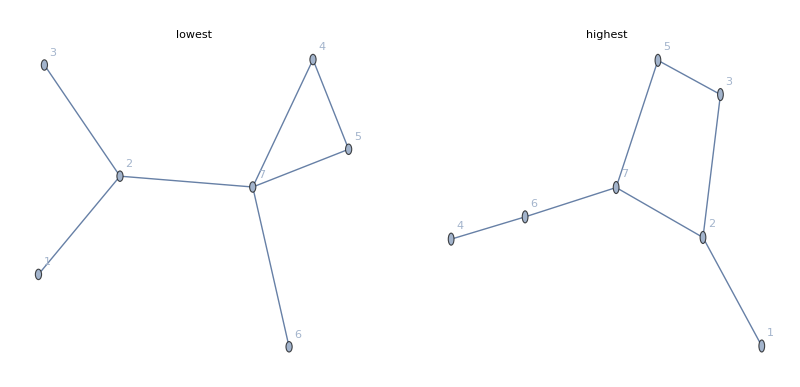

lowest ETE:

0.190651

Coherent Contribution:

1.

Scattering Contribution:

0.

highest ETE:

0.572922

Coherent Contribution:

1.

Scattering Contribution:

0.

0.572922

```mathematica
ω=0;
ETE={};
ETEcoherent={};
ETEscattering={};
Do[
permcoherent=H[perms[[i]],γ];
permLkSet=LindbladSet[permcoherent];
permexits={3};
permtrapping=Trapping[perms[[i]],κ,permexits];
permrecombination=Recombination[perms[[i]],Γ];
permM = SuperOperator[permcoherent,permtrapping,permrecombination,permLkSet,ω,ℏ];
permρ0=SparseArray[{6,6}-> 1,{Length[perms[[i]]],Length[perms[[i]]]}];
AppendTo[ETE,η[permtrapping,permM,permρ0,ℏ]];
AppendTo[ETEcoherent,ηcoherent[permrecombination,permtrapping,permcoherent,permM,permρ0,ℏ,ω]];
AppendTo[ETEscattering,ηscattering[permrecombination,permtrapping,permLkSet,permM,permρ0,ℏ,ω]],
{i,Length[perms]}];
GraphicsRow[{AdjacencyGraph[perms[[Position[ETE,Min[ETE]][[1]][[1]]]],VertexLabels->"Name",PlotLabel->"lowest"],
AdjacencyGraph[perms[[Position[ETE,Max[ETE]][[1]][[1]]]],VertexLabels->"Name",PlotLabel->"highest"]}]
Print["lowest ETE:"]
Min[ETE]
Print["Coherent Contribution:"]
ETEcoherent[[Position[ETE,Min[ETE]][[1]][[1]]]]/Min[ETE]
Print["Scattering Contribution:"]
ETEscattering[[Position[ETE,Min[ETE]][[1]][[1]]]]/Min[ETE]
Print["highest ETE:"]
Max[ETE]
Print["Coherent Contribution:"]
ETEcoherent[[Position[ETE,Max[ETE]][[1]][[1]]]]/Max[ETE]
Print["Scattering Contribution:"]
ETEscattering[[Position[ETE,Max[ETE]][[1]][[1]]]]/Max[ETE]
 Max[ETE]
```

```mathematica
ETEcoherent[[Position[ETE,Max[ETE]][[1]][[1]]]]/Max[ETE]
```

1.

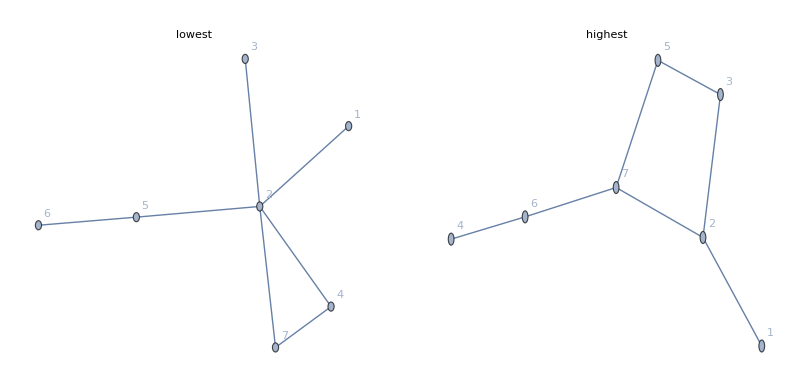

lowest ETE:

0.408381

Coherent Contribution:

0.851393

Scattering Contribution:

0.148607

highest ETE:

0.581096

Coherent Contribution:

1.01815

Scattering Contribution:

-0.0181549

0.581096

```mathematica
ω=0.02;
ETE={};
ETEcoherent={};
ETEscattering={};
Do[
permcoherent=H[perms[[i]],γ];
permLkSet=LindbladSet[permcoherent];
permexits={3};
permtrapping=Trapping[perms[[i]],κ,permexits];
permrecombination=Recombination[perms[[i]],Γ];
permM = SuperOperator[permcoherent,permtrapping,permrecombination,permLkSet,ω,ℏ];
permρ0=SparseArray[{6,6}-> 1,{Length[perms[[i]]],Length[perms[[i]]]}];
AppendTo[ETE,η[permtrapping,permM,permρ0,ℏ]];
AppendTo[ETEcoherent,ηcoherent[permrecombination,permtrapping,permcoherent,permM,permρ0,ℏ,ω]];
AppendTo[ETEscattering,ηscattering[permrecombination,permtrapping,permLkSet,permM,permρ0,ℏ,ω]],
{i,Length[perms]}];
GraphicsRow[{AdjacencyGraph[perms[[Position[ETE,Min[ETE]][[1]][[1]]]],VertexLabels->"Name",PlotLabel->"lowest"],
AdjacencyGraph[perms[[Position[ETE,Max[ETE]][[1]][[1]]]],VertexLabels->"Name",PlotLabel->"highest"]}]
Print["lowest ETE:"]
Min[ETE]
Print["Coherent Contribution:"]
ETEcoherent[[Position[ETE,Min[ETE]][[1]][[1]]]]/Min[ETE]
Print["Scattering Contribution:"]
ETEscattering[[Position[ETE,Min[ETE]][[1]][[1]]]]/Min[ETE]
Print["highest ETE:"]
Max[ETE]
Print["Coherent Contribution:"]
ETEcoherent[[Position[ETE,Max[ETE]][[1]][[1]]]]/Max[ETE]
Print["Scattering Contribution:"]
ETEscattering[[Position[ETE,Max[ETE]][[1]][[1]]]]/Max[ETE]
 Max[ETE]
```

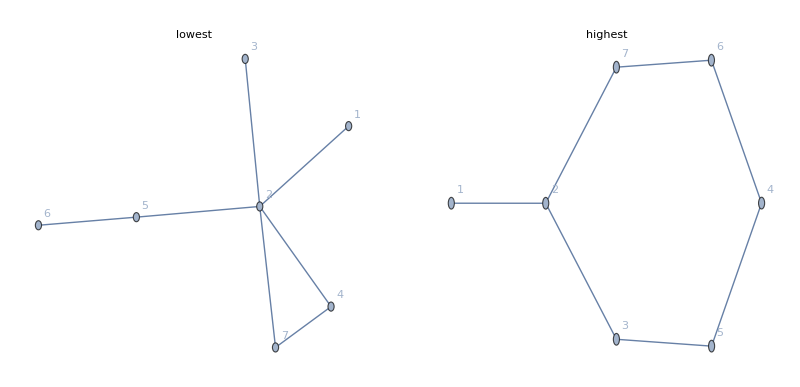

lowest ETE:

0.466235

Coherent Contribution:

0.761073

Scattering Contribution:

0.238927

highest ETE:

0.57905

Coherent Contribution:

0.974125

Scattering Contribution:

0.0258752

0.57905

```mathematica
ω=0.05;
ETE={};
ETEcoherent={};
ETEscattering={};
Do[
permcoherent=H[perms[[i]],γ];
permLkSet=LindbladSet[permcoherent];
permexits={3};
permtrapping=Trapping[perms[[i]],κ,permexits];
permrecombination=Recombination[perms[[i]],Γ];
permM = SuperOperator[permcoherent,permtrapping,permrecombination,permLkSet,ω,ℏ];
permρ0=SparseArray[{6,6}-> 1,{Length[perms[[i]]],Length[perms[[i]]]}];
AppendTo[ETE,η[permtrapping,permM,permρ0,ℏ]];
AppendTo[ETEcoherent,ηcoherent[permrecombination,permtrapping,permcoherent,permM,permρ0,ℏ,ω]];
AppendTo[ETEscattering,ηscattering[permrecombination,permtrapping,permLkSet,permM,permρ0,ℏ,ω]],
{i,Length[perms]}];
GraphicsRow[{AdjacencyGraph[perms[[Position[ETE,Min[ETE]][[1]][[1]]]],VertexLabels->"Name",PlotLabel->"lowest"],
AdjacencyGraph[perms[[Position[ETE,Max[ETE]][[1]][[1]]]],VertexLabels->"Name",PlotLabel->"highest"]}]
Print["lowest ETE:"]
Min[ETE]
Print["Coherent Contribution:"]
ETEcoherent[[Position[ETE,Min[ETE]][[1]][[1]]]]/Min[ETE]
Print["Scattering Contribution:"]
ETEscattering[[Position[ETE,Min[ETE]][[1]][[1]]]]/Min[ETE]
Print["highest ETE:"]
Max[ETE]
Print["Coherent Contribution:"]
ETEcoherent[[Position[ETE,Max[ETE]][[1]][[1]]]]/Max[ETE]
Print["Scattering Contribution:"]
ETEscattering[[Position[ETE,Max[ETE]][[1]][[1]]]]/Max[ETE]
 Max[ETE]
```

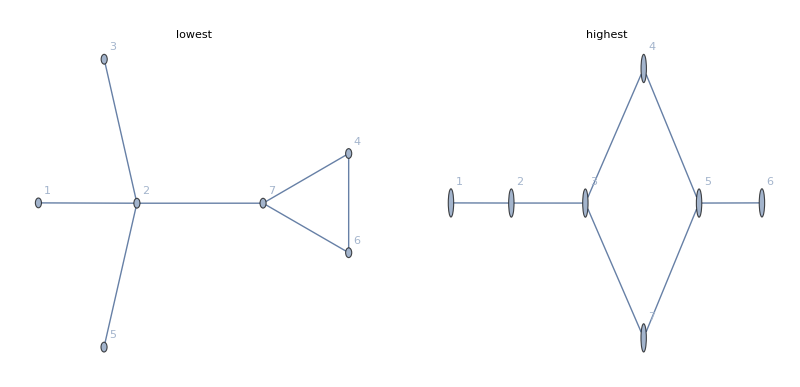

lowest ETE:

0.520593

Coherent Contribution:

0.486182

Scattering Contribution:

0.513818

highest ETE:

0.568449

Coherent Contribution:

0.72994

Scattering Contribution:

0.27006

0.568449

```mathematica
ω=0.25;
ETE={};
ETEcoherent={};
ETEscattering={};
Do[
permcoherent=H[perms[[i]],γ];
permLkSet=LindbladSet[permcoherent];
permexits={3};
permtrapping=Trapping[perms[[i]],κ,permexits];
permrecombination=Recombination[perms[[i]],Γ];
permM = SuperOperator[permcoherent,permtrapping,permrecombination,permLkSet,ω,ℏ];
permρ0=SparseArray[{6,6}-> 1,{Length[perms[[i]]],Length[perms[[i]]]}];
AppendTo[ETE,η[permtrapping,permM,permρ0,ℏ]];
AppendTo[ETEcoherent,ηcoherent[permrecombination,permtrapping,permcoherent,permM,permρ0,ℏ,ω]];
AppendTo[ETEscattering,ηscattering[permrecombination,permtrapping,permLkSet,permM,permρ0,ℏ,ω]],
{i,Length[perms]}];
GraphicsRow[{AdjacencyGraph[perms[[Position[ETE,Min[ETE]][[1]][[1]]]],VertexLabels->"Name",PlotLabel->"lowest"],
AdjacencyGraph[perms[[Position[ETE,Max[ETE]][[1]][[1]]]],VertexLabels->"Name",PlotLabel->"highest"]}]
Print["lowest ETE:"]
Min[ETE]
Print["Coherent Contribution:"]
ETEcoherent[[Position[ETE,Min[ETE]][[1]][[1]]]]/Min[ETE]
Print["Scattering Contribution:"]
ETEscattering[[Position[ETE,Min[ETE]][[1]][[1]]]]/Min[ETE]
Print["highest ETE:"]
Max[ETE]
Print["Coherent Contribution:"]
ETEcoherent[[Position[ETE,Max[ETE]][[1]][[1]]]]/Max[ETE]
Print["Scattering Contribution:"]
ETEscattering[[Position[ETE,Max[ETE]][[1]][[1]]]]/Max[ETE]
 Max[ETE]
```

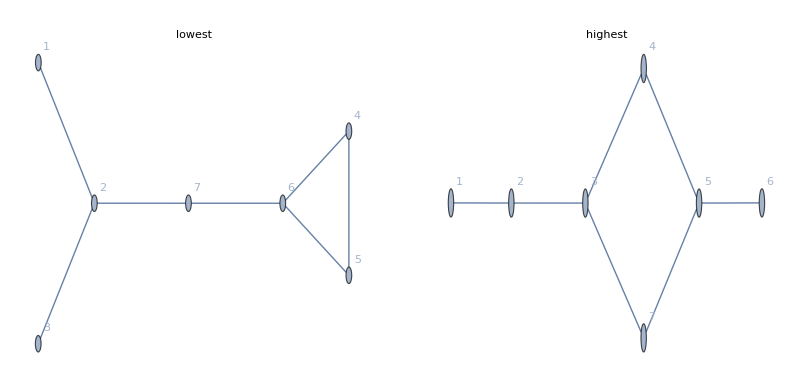

lowest ETE:

0.521151

Coherent Contribution:

0.58683

Scattering Contribution:

0.41317

highest ETE:

0.567653

Coherent Contribution:

0.693125

Scattering Contribution:

0.306875

0.567653

```mathematica
ω=0.27;
ETE={};
ETEcoherent={};
ETEscattering={};
Do[
permcoherent=H[perms[[i]],γ];
permLkSet=LindbladSet[permcoherent];
permexits={3};
permtrapping=Trapping[perms[[i]],κ,permexits];
permrecombination=Recombination[perms[[i]],Γ];
permM = SuperOperator[permcoherent,permtrapping,permrecombination,permLkSet,ω,ℏ];
permρ0=SparseArray[{6,6}-> 1,{Length[perms[[i]]],Length[perms[[i]]]}];
AppendTo[ETE,η[permtrapping,permM,permρ0,ℏ]];
AppendTo[ETEcoherent,ηcoherent[permrecombination,permtrapping,permcoherent,permM,permρ0,ℏ,ω]];
AppendTo[ETEscattering,ηscattering[permrecombination,permtrapping,permLkSet,permM,permρ0,ℏ,ω]],
{i,Length[perms]}];
GraphicsRow[{AdjacencyGraph[perms[[Position[ETE,Min[ETE]][[1]][[1]]]],VertexLabels->"Name",PlotLabel->"lowest"],
AdjacencyGraph[perms[[Position[ETE,Max[ETE]][[1]][[1]]]],VertexLabels->"Name",PlotLabel->"highest"]}]
Print["lowest ETE:"]
Min[ETE]
Print["Coherent Contribution:"]
ETEcoherent[[Position[ETE,Min[ETE]][[1]][[1]]]]/Min[ETE]
Print["Scattering Contribution:"]
ETEscattering[[Position[ETE,Min[ETE]][[1]][[1]]]]/Min[ETE]
Print["highest ETE:"]
Max[ETE]
Print["Coherent Contribution:"]
ETEcoherent[[Position[ETE,Max[ETE]][[1]][[1]]]]/Max[ETE]
Print["Scattering Contribution:"]
ETEscattering[[Position[ETE,Max[ETE]][[1]][[1]]]]/Max[ETE]
 Max[ETE]
```

```mathematica
ω=1.0;
ETE={};
ETEcoherent={};
ETEscattering={};
Do[
permcoherent=H[perms[[i]],γ];
permLkSet=LindbladSet[permcoherent];
permexits={3};
permtrapping=Trapping[perms[[i]],κ,permexits];
permrecombination=Recombination[perms[[i]],Γ];
permM = SuperOperator[permcoherent,permtrapping,permrecombination,permLkSet,ω,ℏ];
permρ0=SparseArray[{6,6}-> 1,{Length[perms[[i]]],Length[perms[[i]]]}];
AppendTo[ETE,η[permtrapping,permM,permρ0,ℏ]];
AppendTo[ETEcoherent,ηcoherent[permrecombination,permtrapping,permcoherent,permM,permρ0,ℏ,ω]];
AppendTo[ETEscattering,ηscattering[permrecombination,permtrapping,permLkSet,permM,permρ0,ℏ,ω]],
{i,Length[perms]}];
GraphicsRow[{AdjacencyGraph[perms[[Position[ETE,Min[ETE]][[1]][[1]]]],VertexLabels->"Name",PlotLabel->"lowest"],
AdjacencyGraph[perms[[Position[ETE,Max[ETE]][[1]][[1]]]],VertexLabels->"Name",PlotLabel->"highest"]}]
Print["lowest ETE:"]
Min[ETE]
Print["Coherent Contribution:"]
ETEcoherent[[Position[ETE,Min[ETE]][[1]][[1]]]]/Min[ETE]
Print["Scattering Contribution:"]
ETEscattering[[Position[ETE,Min[ETE]][[1]][[1]]]]/Min[ETE]
Print["highest ETE:"]
Max[ETE]
Print["Coherent Contribution:"]
ETEcoherent[[Position[ETE,Max[ETE]][[1]][[1]]]]/Max[ETE]
Print["Scattering Contribution:"]
ETEscattering[[Position[ETE,Max[ETE]][[1]][[1]]]]/Max[ETE]
 Max[ETE]
```

-Graphics-

lowest ETE:

0.538113

Coherent Contribution:

0.

Scattering Contribution:

1.

highest ETE:

0.570668

Coherent Contribution:

0.

Scattering Contribution:

1.

0.570668

```mathematica
Table[Count[Eigenvectors[H[perms[[i]],1]][[;;,3]],0],{i,32}]
```

{1,0,1,0,1,1,2,0,1,0,1,0,1,2,0,2,0,0,2,1,1,0,2,2,0,1,2,1,2,2,2,0}

```mathematica
a[[28]]
```

6.43574

```mathematica
N[Eigenvectors[H[perms[[7]],1]]]//MatrixForm
```

(0.130901 | -0.557875 | 0.130901 | -0.234643 | -0.234643 | -0.234643 | 1.
-0.830062 | 1.94224 | -0.830062 | -0.427373 | -0.427373 | -0.427373 | 1.
0. | 0. | 0. | -1. | 1. | 0. | 0.
0. | 0. | 0. | -1. | -1. | 2. | 0.
-1. | 0. | 1. | 0. | 0. | 0. | 0.
-2.30084 | -1.38437 | -2.30084 | 1.66202 | 1.66202 | 1.66202 | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1.)

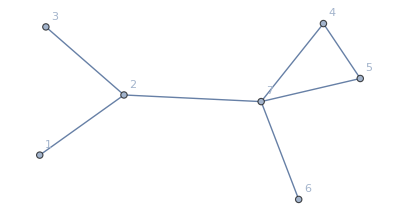

```mathematica
AdjacencyGraph[perms[[7]],VertexLabels->"Name"]
```

```mathematica
N[Eigenvectors[H[perms[[7]],1]][[;;,#]]&/@Flatten[Position[perms[[7]][[3]],1]]]
```

{{-0.557875,1.94224,0.,0.,0.,-1.38437,1.}}

```mathematica
Table[Min[Count[Eigenvectors[H[perms[[i]],1]][[;;,#]],0]&/@Flatten[Position[perms[[i]][[3]],1]]],{i,32}]
```

{1,0,1,0,0,2,3,1,2,0,2,1,1,0,0,0,0,0,3,2,2,1,3,3,0,1,3,2,3,2,2,0}

```mathematica
Position[perms[[7]][[3]],1]
```

{{2}}

```mathematica
perms[[7]][[3]]
```

{0,1,0,0,0,0,0}